# From the Master Equation to the Kraus Decomposition

```mathematica
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
```

#### Hermitian Basis of operators on H_2

```mathematica
G=1/(√2){PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
```

#### Computational Basis of operators on H_2

```mathematica
F={({{1, 0}, {0, 0}}),({{0, 1}, {0, 0}}),({{0, 0}, {1, 0}}),({{0, 0}, {0, 1}})};
```

### The GKSL Master Equation on H_2

```mathematica
Comm[A_, B_]:=A.B-B.A
```

```mathematica
L[x_, H_,A_]:=-ⅈ*Comm[H,x]+1/2 Sum[A[[k,l]]*(Comm[G[[k+1]],x.G[[l+1]]]+Comm[G[[k+1]].x,G[[l+1]]]),{k,1,3},{l,1,3}]
```

#### The Matrix representation for the GKSL operator

```mathematica
LiouvillianMatrix[H_,A_]:=Module[{M},M=Table[Tr[G[[i]].L[G[[j]],H,A]],{i,1,4},{j,1,4}];
Simplify[M]];
```

#### The positive matrix A for spontaneous emission

```mathematica
A=x/4({{1, -ⅈ, 0}, {ⅈ, 1, 0}, {0, 0, 0}});
```

#### The Matrix representation for the spontaneous emission Master Equation

```mathematica
H=10*F[[4]];
```

```mathematica
matL=LiouvillianMatrix[H,A]
```

(0 | 0 | 0 | 0
0 | -x/4 | 10 | 0
0 | -10 | -x/4 | 0
x/2 | 0 | 0 | -x/2)

#### The matrix Representation for the CPTP map associated to Spontaneous emission

```mathematica
matE=FullSimplify[MatrixExp[t*matL]]
```

(1 | 0 | 0 | 0
0 | ⅇ^(-(t x)/4) Cos[10 t] | ⅇ^(-(t x)/4) Sin[10 t] | 0
0 | -ⅇ^(-(t x)/4) Sin[10 t] | ⅇ^(-(t x)/4) Cos[10 t] | 0
1-ⅇ^(-(t x)/2) | 0 | 0 | ⅇ^(-(t x)/2))

## Constructing the Choi-Jamiołkowski Representation of the CPTP map

```mathematica
U=Table[Tr[G[[i]].F[[j]]],{i,1,4},{j,1,4}]
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | ⅈ/(√2) | -ⅈ/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2))

```mathematica
B=FullSimplify[matE.U]
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | ⅇ^(-1/4 t (-40 ⅈ+x))/(√2) | ⅇ^(-1/4 t (40 ⅈ+x))/(√2) | 0
0 | (ⅈ ⅇ^(-1/4 t (-40 ⅈ+x)))/(√2) | -(ⅈ ⅇ^(-1/4 t (40 ⅈ+x)))/(√2) | 0
1/(√2) | 0 | 0 | (1-2 ⅇ^(-(t x)/2))/(√2))

```mathematica
J=FullSimplify[1/2*Sum[B[[k,l]]* KroneckerProduct[G[[k]],F[[l]]],{k,1,4},{l,1,4}], Assumptions->t>0&&x>0&& ω∈ Reals]
```

(1/2 | 0 | 0 | 1/2 ⅇ^(-1/4 t (-40 ⅈ+x))
0 | 1/2-1/2 ⅇ^(-(t x)/2) | 0 | 0
0 | 0 | 0 | 0
1/2 ⅇ^(-1/4 t (40 ⅈ+x)) | 0 | 0 | 1/2 ⅇ^(-(t x)/2))

```mathematica
{vals,vecs}=FullSimplify[Eigensystem[J],Assumptions->t>0&&x>0]
```

{{0,0,1/2-1/2 ⅇ^(-(t x)/2),1/2 (1+ⅇ^(-(t x)/2))},{{-ⅇ^(-1/4 t (-40 ⅈ+x)),0,0,1},{0,0,1,0},{0,1,0,0},{ⅇ^(1/4 t (40 ⅈ+x)),0,0,1}}}

```mathematica
vecs=FullSimplify[Normalize/@vecs,Assumptions->t ∈ Reals && x ∈ Reals]
```

(-ⅇ^(-1/4 t (-40 ⅈ+x))/(√(1+ⅇ^(-(t x)/2))) | 0 | 0 | 1/(√(1+ⅇ^(-(t x)/2)))
0 | 0 | 1 | 0
0 | 1 | 0 | 0
ⅇ^(1/4 t (40 ⅈ+x))/(√(1+ⅇ^((t x)/2))) | 0 | 0 | 1/(√(1+ⅇ^((t x)/2))))

### Extracting the Kraus operators

```mathematica
GenerateKrausOperators[vals_List,vecs_List]:=Module[{n,K},n=Sqrt[Length[vecs[[1]]]]//Round;
K=FullSimplify[Table[Sqrt[2 vals[[i]]] ArrayReshape[vecs[[i]],{n,n}],{i,Length[vals]}]]];
```

```mathematica
Kraus=GenerateKrausOperators[vals,vecs];
```

```mathematica
Kraus[[1]]
```

(0 | 0
0 | 0)

```mathematica
Kraus[[2]]
```

(0 | 0
0 | 0)

```mathematica
Kraus[[3]]
```

(0 | √(1-ⅇ^(-(t x)/2))
0 | 0)

```mathematica
FullSimplify[Kraus[[4]], Assumptions->t ∈ Reals && x ∈ Reals]
```

(ⅇ^(10 ⅈ t) | 0
0 | ⅇ^(-(t x)/4))

### The action of the CPTP map on some density matrices

```mathematica
CPTP[ρ_]:= Sum[Kraus[[i]].ρ.ConjugateTranspose[Kraus[[i]]],{i,3,4}]
```

#### The ground state is invariant under spontaneous emission

```mathematica
ρ=({{1, 0}, {0, 0}});
FullSimplify[CPTP[ρ],Assumptions->t ∈ Reals && x ∈ Reals]
```

(1 | 0
0 | 0)

### The exited state

```mathematica
ρ=({{0, 0}, {0, 1}});
sigma=FullSimplify[CPTP[ρ],Assumptions->t >0 && x >0]
```

(1-ⅇ^(-(t x)/2) | 0
0 | ⅇ^(-(t x)/2))

```mathematica
sigma=sigma/.{x->1}
```

(1-ⅇ^(-t/2) | 0
0 | ⅇ^(-t/2))

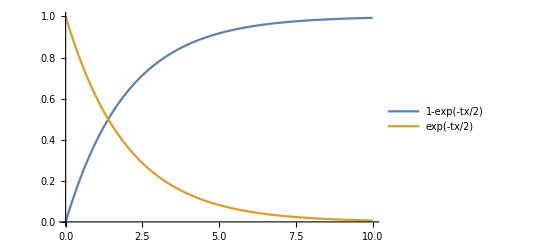

```mathematica
Plot[{sigma[[1,1]],sigma[[2,2]]},{t,0,10}, PlotLegends->{HoldForm[1-Exp[-tx/2]],HoldForm[Exp[-tx/2]]}]
```

```mathematica
ρ=1/2({{1, 1}, {1, 1}});
```

```mathematica
sigma=FullSimplify[CPTP[ρ],Assumptions->t >0 && x >0]
```

(1-1/2 ⅇ^(-(t x)/2) | 1/2 ⅇ^(-1/4 t (-40 ⅈ+x))
1/2 ⅇ^(-1/4 t (40 ⅈ+x)) | 1/2 ⅇ^(-(t x)/2))

```mathematica
sigma=sigma/.{x->5}
```

(1-1/2 ⅇ^(-5 t/2) | 1/2 ⅇ^((-5/4+10 ⅈ) t)
1/2 ⅇ^((-5/4-10 ⅈ) t) | 1/2 ⅇ^(-5 t/2))

```mathematica
Pplus=1/2({{1, 1}, {1, 1}});
Pminus=1/2({{1, -1}, {-1, 1}});
```

```mathematica
probplus=Tr[sigma.Pplus];
probminus=Tr[sigma.Pminus];
```

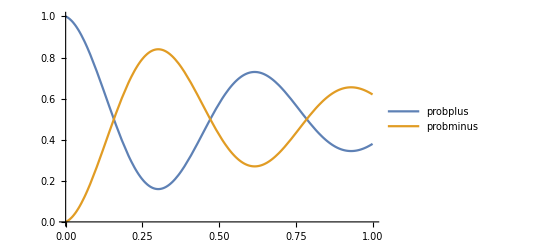

```mathematica
Plot[{probplus,probminus},{t,0,1}, PlotLegends->"Expressions", PlotRange->Full]
```

```mathematica
X=FullSimplify[Tr[sigma.PauliMatrix[1]]]
```

ⅇ^(-5 t/4) Cos[10 t]

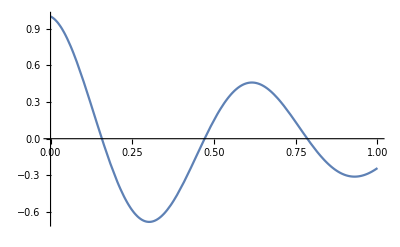

```mathematica
Plot[X,{t,0,1}]
```